```mathematica
(*Set to True to enable status printing*)
printStatus = False;

(*Set to True to find and export the Trilinear and Top Yukawa*)
addTrilin = False;

(*Enable to ignore lax constraints*)
overWriteLAXConstr=True;
```

## Initializations

```mathematica
(* Initialise the Machine 0 *)
machineZero = 10^(-$MachinePrecision);

(* Mass Approximations for all the Bessel Equations*)
mWboson[k_, zL_, θH_]:=Sqrt[3/2] * k *((zL)^(-3/2)) * Sin[θH];
mZboson[mWboson_, sin2θW_]:=mWboson / Sqrt[1-sin2θW];
muTypeQuark[c0_, k_, zL_,θH_ ]:=If[c0< 0.5,
 (k/zL )*Sqrt[1 - 4 (c0)^2]Sin[θH/2],
 k *((zL)^-1/2 - c0)*Sqrt[4(c0)^2 - 1]Sin[θH/2]
];
mdTypeQuark[c0_, c1_, μ11_, μ1_, k_, zL_, θH_]:=If[c0<0.5,
k * ((zL)^(c0-c1-1)) * μ11/μ1*Sqrt[(1-2c0)(1+2c1)]*Sin[θH/2],
k * ((zL)^(-c1-1/2)) * μ11/μ1*Sqrt[(2c0 - 1)(2c1 + 1)]*Sin[θH/2]
];
meTypeLepton[c2_, c0_, μ11Prime_, μ2Tilde_, k_, zL_, θH_]:=If[ c2<0.5,
k * ((zL)^(-1+c2-c0)) * μ11Prime/μ2Tilde Sqrt[(2c0 + 1)(1-2c2)]Sin[θH/2],
k *  ((zL)^(-1/2 - c0)) * μ11Prime/μ2Tilde Sqrt[(2c0+1)(2c2-1)]Sin[θH/2]
];
mPsiDarkType[c0Prime_, k_, zL_, θH_]:=If[c0Prime< 0.5,
 k *(zL^(-1))Sqrt[1 - 4 (c0Prime)^2]Cos[θH/2],
 k *(zL^(-1/2 - c0Prime))Sqrt[4(c0Prime)^2 - 1]Cos[θH/2]
];
mνType [mu_, M_, mB_, c0_, zL_]:=-(2(mu)^2 *M* ((zL)^(2c0 + 1)))/((2c0 + 1) *(mB^2));



(*Bessel basis functions Subscript[FHat, αβ],Subscript[F, αβ] *)
Fab[α_, β_, u_, v_]:=BesselJ[α, u] BesselY[β, v] - BesselY[α, u]BesselJ[β, v];
FHat[α_, β_, u_, v_]:=BesselI[α, u] * BesselK[β, v] - Exp[-ⅈ(α - β ) * Pi] * BesselK[α,u] * BesselI[β,v];
FHatcPM[q_, c_, pm1_, pm2_, zL_]:=FHat[ c + pm1*1/2, c+pm2*1/2, q*(zL^(-1)), q  ];
(*   Fermions  *)
SL[λ_, z_, zL_, c_]:=-π/2 λ Sqrt[z zL]Fab[c+1/2, c+1/2, λ z, λ zL];
SR[λ_, z_, zL_, c_]:= (+π)/2 λ Sqrt[z zL]Fab[c-1/2, c-1/2, λ z, λ zL];
CR[λ_, z_, zL_, c_]:=-π/2 λ Sqrt[z zL]Fab[c-1/2, c+1/2, λ z, λ zL];
CL[λ_, z_, zL_, c_]:=(+π)/2 λ Sqrt[z zL]Fab[c+1/2, c-1/2, λ z, λ zL];

(*   Bosons   *)
Cbasis[λ_, z_, zL_]:=π/2 λ (z^(3/2)) (zL^(1/2)) Fab[3/2, 1/2, λ z, λ zL];
Sbasis[λ_, z_, zL_]:=-π/2 λ (z^(3/2)) (zL^(1/2)) Fab[3/2, 3/2, λ z ,λ zL];
Cprime[λ_, z_, zL_]:=π/2(λ^2) (z^(3/2)) (zL^(1/2)) Fab[1/2, 1/2, λ z, λ zL];
Sprime[λ_, z_, zL_]:=-π/2(λ^2) (z^(3/2)) (zL^(1/2))Fab[1/2, 3/2, λ z, λ zL];

(* EffectivePotential Auxiliaries*)
IntIfct[Q_, f_, q_]:= q^3 Log[1+Q*f ];
IntConst[k_, zL_] := N[(k/zL)^4/(4π)^2];
Q0[q_, c_, zL_]:= (zL/(q^2)) * (1/(FHatcPM[q, c, 1, 1, zL]*FHatcPM[q, c, -1, -1, zL]));


Qii[q_,c0_,c1_,μ1_, μ11_, zL_]:=(zL/(q^2))*( FHatcPM[q,c0,1, 1, zL]*FHatcPM[q,c0,-1, -1, zL] + ((μ1^2) *FHatcPM[q,c0,-1, -1, zL]*FHatcPM[q,c0,-1, 1, zL]*FHatcPM[q,c1,1, 1,zL]*FHatcPM[q,c1,-1, 1, zL] )/((μ11^2) * (FHatcPM[q,c1,-1, 1, zL])^2 +( FHatcPM[q,c1,1, 1, zL])^2) )^(-1);


Qiii[q_,c0_,c2_,μ2Tilde_, μ11Prime_, zL_]:= (zL/(q^2))*(FHatcPM[q,c0,1, 1, zL] * FHatcPM[q,c0,-1, -1, zL]  + ((μ2Tilde^2)*FHatcPM[q,c0,1, 1, zL]*FHatcPM[q,c0,1, -1, zL]*FHatcPM[q,c2,-1, -1, zL]*FHatcPM[q,c2,1, -1, zL])/((μ11Prime^2) * (FHatcPM[q,c2,1, -1, zL])^2 + (FHatcPM[q,c2,-1, -1, zL])^2) )^(-1)  ;



Qiv1Aux[q_,c0_,mB_, M_ , zL_, k_]:= (zL/(q^2))*(FHatcPM[q,c0,1, 1, zL] * FHatcPM[q,c0,-1, -1, zL]  - (ⅈ* (mB^2) / (k^2))/(2(ⅈ* q* (zL)^(-1) + M/k))*FHatcPM[q,c0,-1, 1, zL]*FHatcPM[q,c0,-1, -1, zL])^(-1);
Qiv1[QAux_, θH_]:=Simplify[(QAux + Conjugate[QAux])] * (Sin[1/2 θH])^2 + Simplify[QAux * Conjugate[QAux]] * (Sin[1/2 θH])^4;



h1[q_, θH_, μ11Prime_, c2_, zL_] :=(1-μ11Prime^2)(2 * (q^2)/(zL)(1+μ11Prime^2) * FHatcPM[q,c2,1, 1, zL]*FHatcPM[q,c2,-1, -1, zL] + 2μ11Prime^2 + (1-μ11Prime^2)*(Sin[θH])^2 ) * (Sin[θH])^2;
h2[q_,  μ11Prime_, c2_, zL_]:=((zL^2)/(q^4))* μ11Prime^4 + 2μ11Prime^4 * (zL/(q^2))*FHatcPM[q,c2,1, 1, zL]*FHatcPM[q,c2,-1, -1, zL] + 
(1+μ11Prime^4)(FHatcPM[q,c2,1, 1, zL]*FHatcPM[q,c2,-1, -1, zL])^2 +
μ11Prime^2( (FHatcPM[q,c2,-1, 1, zL]*FHatcPM[q,c2,-1, -1, zL])^2 + (FHatcPM[q,c2,1, -1, zL]*FHatcPM[q,c2,1, 1, zL])^2 );
Qiv2[q_, θH_, μ11Prime_, c2_, zL_]:=((zL^2)/(q^4))* h1[q, θH, μ11Prime, c2, zL]/h2[q, μ11Prime, c2, zL];

(* Higgs Mass Auxiliaries*)
fHfunc[k_, zL_, sin2θW_, αEM_]:=Sqrt[ (6* sin2θW) /(4 * Pi * αEM)] * (k/Sqrt[ (1-1/zL)*(zL^3 - 1) ]);
findθHMinRule[VeffFCT_, q_, θH_] := Quiet[FindMinimum[  
Quiet[NIntegrate [VeffFCT /.{θH->θHLocal}, {q, 0, ∞}]], {θHLocal,0,1}  
][[2]]];
μ11Fct[μ1_,zL_,c0_,c1_]:=(4.18/172.44)*μ1*(1/(zL^(c0-c1)))*Sqrt[(1+2 c0)/(1+2 c1)];
μ11PrimeFct[μ2Tilde_,zL_,c0_,c2_]:=Which[
c0<0.5 && c2<0.5,
(1.776/172.44)*μ2Tilde*(1/(zL^(c2-c0)))*Sqrt[(1-2 c0)/(1-2 c2)],
c0<0.5&&c2>0.5,
(1.776/172.44) *μ2Tilde*(1/(zL^(0.5-c0)))*Sqrt[(1-2 c0)/(2 c2-1)],
c0>0.5&&c2<0.5,
(1.776/172.44) *μ2Tilde*(1/(zL^(c2-0.5)))*Sqrt[(2 c0-1)/(1-2 c2)],
c0>0.5&&c2>0.5,
(1.776/172.44) *μ2Tilde*Sqrt[(2 c0-1)/(2 c2-1)]
];


(**   Auxiliaries **)

return0Masses[]:={"Higgs"->0.0,"mTop"->0.0,"mBottom"->0.0,"mTau"->0.0,"mNeutrino"->0.0,"mPsiDark"->0.0,"ThetaHiggs"->0.0,"mWpm"->0.0,"mZ0"->0.0,"mZprime"->0.0, "Triviality"-> 1};


evalConstr[strParticle_, particleMass_]:=If[
constrList[strParticle]["Max"]> particleMass > constrList[strParticle]["Min"],
Return[True];
,
Return[False];
];

esc=Association["reset"->"\033[1;0m","black"->"\033[1;30m","red"->"\033[1;31m","green"->"\033[1;32m","yellow"->"\033[1;33m","blue"->"\033[1;34m","magenta"->"\033[1;35m"];

printMessage[startStopBool_, particleStr_]:= Module[{},
If[startStopBool, colorANSI = esc["blue"]; startStopStr = "Started";, colorANSI = esc["green"];startStopStr = "Finished"];

Print["\n---------------------------------------------------------------------------------------------------"];
Print[colorANSI,startStopStr,esc["reset"],": Finding ",esc["yellow"],particleStr,esc["reset"]," Solutions"];
Print["---------------------------------------------------------------------------------------------------\n"];
]
```

## Effective potential V_eff(θH) and Higgs Derivative.

```mathematica
(***  Up-type quark contribution ***)
VeffiFCT[q_, c0_,k_, zL_, θH_, realsList_]:= Simplify[ -12 *IntConst[k, zL] *  IntIfct[Q0[q, c0, zL], (Sin[θH/2])^2, q], {realsList∈Reals}] ;

(***  Down-type quark contribution ***)
VeffiiFCT[k_, zL_, q_, c0_, c1_, μ1_, μ11_,θH_, realsList_] :=Simplify[  -12 * IntConst[k, zL] *IntIfct[Qii[q, c0, c1, μ1, μ11, zL],(Sin[θH/2])^2, q ], { realsList∈Reals}] ;

(***  Lepton contribution contribution ***)
VeffiiiFCT[k_, zL_, q_, c0_, c2_, μ2Tilde_, μ11Prime_, θH_,  realsList_] := Simplify[-4 * IntConst[k, zL] * IntIfct[ Qiii[q, c0, c2, μ2Tilde, μ11Prime, zL],(Sin[θH/2])^2, q ] ,  {realsList∈Reals} ];

(***   Neutrino Sector  ***)
Veffiv1FCT[k_, zL_, q_, c0_, mB_, M_, θH_,  realsList_] := Simplify[-4/2 * IntConst[k, zL] * IntIfct[ Qiv1[ Qiv1Aux[q, c0, mB, M, zL, k], θH ] , 1, q] ,  {realsList∈Reals} ];
Veffiv2FCT[k_, zL_, q_, θH_, μ11Prime_, c2_,  realsList_] :=Simplify[-4 * IntConst[k, zL] * IntIfct[ Qiv2[q, θH, μ11Prime, c2, zL], 1, q] ,
{realsList∈Reals} ];


(***   Dark Fermion Contribution  ***)
VeffvFCT[k_, zL_, q_, c0Prime_, θH_,  realsList_] :=Simplify[-32 * IntConst[k, zL] * IntIfct[ Q0[q, c0Prime, zL], (Cos[θH/2])^2, q] ,
{realsList∈Reals} ];
VeffWpmFCT[ξGauge_, k_, zL_, q_, θH_]:=Simplify[2(3-ξGauge^2) * IntConst[k, zL] * IntIfct[1/2*Q0[q, 1, zL], (Sin[θH])^2,q] ,
{realsList∈Reals}  ] ;
VeffZFCT[ξGauge_, k_, zL_, q_, sin2θW_, θH_]:= Simplify [(3-ξGauge^2) * IntConst[k, zL] * IntIfct[Q0[q, 1, zL]/(2(1-sin2θW)),(Sin[θH])^2,q],
{realsList∈Reals }];
VeffAzFCT[ξGauge_, k_ , zL_, q_, θH_]:=Simplify[3ξGauge^2 * IntConst[k, zL] *  IntIfct[ Q0[q, 1, zL],(Sin[θH])^2,q ],
{realsList∈Reals } ];
Clear[zL, k, μ11, μ1,μ11Prime, μ2Tilde, c0Prime, c0,c1, c2, θHRule, θHmin, sin2θW, ξGauge, M, mB, αEM, fH, θH];
realsList = {q, c0, c1,c2 , μ1, μ11,μ2Tilde,μ11Prime,mB, M, θH, zL, k};

VeffFermionFCT =VeffiFCT[q, c0,k, zL, θH, realsList]  +
			 VeffiiFCT[k, zL, q, c0, c1, μ1, μ11,θH, realsList]+
			 VeffiiiFCT[k, zL, q, c0, c2, μ2Tilde, μ11Prime, θH,  realsList]+
				Veffiv1FCT[k, zL, q, c0, mB, M, θH,  realsList]+
				Veffiv2FCT[k, zL, q, θH, μ11Prime, c2,  realsList] +
			VeffvFCT[k, zL, q, c0Prime, θH,  realsList];
VeffBosonFct=VeffWpmFCT[ξGauge, k, zL, q, θH] +
		       VeffZFCT[ξGauge, k, zL, q, sin2θW, θH] + 
		       VeffAzFCT[ξGauge, k , zL, q, θH];


VeffFCT = VeffFermionFCT + VeffBosonFct;
HiggsDeriv = D[VeffFCT, {θH,2}];
HiggsDeriv3 = D[VeffFCT, {θH,3}];
HiggsDeriv4 = D[VeffFCT, {θH,4}];
```

## Parameter Declarations And Higgs Computation

```mathematica
SetSystemOptions["MachineRealPrintPrecision"->Round[$MachinePrecision]];
Clear[zL,k,μ11,μ1,μ11Prime,μ2Tilde,c0Prime,c0,c1,c2,θHRule,θHmin,sin2θW,ξGauge,M,mB,αEM,fH,λListTop];


timeOut=60;
timeOutSolve = 60;

(* Uncomment below in the .m file *)
(*JsonNb=$ScriptCommandLine[[2]];
jsonName="dataIn"<>JsonNb<>".json";
jsonNameOut="massesOut"<>JsonNb<>".json";*)

(*Comment out in the .m, file*)
SetDirectory[NotebookDirectory[]];

jsonName = "dataInThreadNb-0.json";
jsonNameOut="massesOutThreadNb-0.json";


(* Constant setting function.*)
sin2θW=0.2312;
ξGauge=0;
M=-10^7;
mB=1.145*10^12;
αEM=1/127.96;
fH = fHfunc[k, zL, sin2θW, αEM];


(*dataRule=Import[jsonName];
k="k"/.dataRule;
zL="zL"/.dataRule;
c0="c0"/.dataRule;
c1="c1"/.dataRule;
c2="c2"/.dataRule;
c0Prime="c0Prime"/.dataRule;

μ1="Mu1"/.dataRule;
μ2Tilde="Mu2Tilde"/.dataRule;

μ11="Mu11"/.dataRule;
μ11Prime="Mu11Prime"/.dataRule;*)


(*k= 89130;                             
zL =35; 
c0 =0.3325; 
c1 =0.0;
c2 =-0.7;
c0Prime =0.5224;

μ1 =11.18;
μ2Tilde =0.7091;

μ11=0.108;
μ11Prime=0.108;*)


k= 266559.06;                             
zL =35; 
c0 =0.3289; 
c1 =0.0;
c2 =-0.7;
c0Prime =0.5960;


μ11=0.1730;
μ11Prime=0.1730;

μ2Tilde =1.138;
μ1 =Sqrt[(1+2 c1)/(1 + 2 c0)]*zL^(c0-c1) * (172.44/4.18)*μ11;

mKK5 = π k /(zL-1);
replacementRules = {z->1, c0var->c0, zLvar->zL, μ1var -> μ1, μ11var -> μ11, c1var -> c1, μ2TildeVar -> μ2Tilde, μ11PrimeVar -> μ11Prime, c2var -> c2, c0PrimeVar -> c0Prime};

(*Tower Declarations*)
SL0 = SL[λ, z, zLvar, c0var];
SR0 = SR[λ, z, zLvar, c0var];
CR0 = CR[λ, z, zLvar, c0var];
CL0 =  CL[λ, z, zLvar, c0var];
SL1 = SL[λ, z, zLvar, c1var];
CR1 = CR[λ, z, zLvar, c1var];
SR2 = SR[λ, z, zLvar, c2var];
CL2 = CL[λ, z, zLvar, c2var];
SL0prime = SL[λ, z, zLvar, c0PrimeVar];
SR0prime = SR[λ, z, zLvar, c0PrimeVar];


uQuarkSol = SL0 * SR0  + (Sin[θHmin/2])^2/.replacementRules;
bQuarkSol = SL0 * SR0  + (Sin[θHmin/2])^2+((μ1var^2) SR0* CR0 * SL1 *CR1)/(μ11var^2 (CR1)^2 - (SL1)^2)/.replacementRules;
tauLeptonSol = SL0 * SR0  + (Sin[θHmin/2])^2+ (μ2TildeVar^2 SL0 CL0 SR2 CL2) / (μ11PrimeVar^2 (CL2)^2  - (SR2)^2) /.replacementRules;
psiDarkQuarkSol = SL0prime * SR0prime + (Cos[θHmin/2])^2/.replacementRules;
WbosonSol = (2* Cprime[λ, z, zLvar]*Sbasis[λ, z, zLvar] + λ (Sin[θHmin])^2)/.replacementRules;
WRSol = Cbasis[λ, z, zLvar] /.replacementRules;
γTower = Cprime[λ, z, zLvar]/.replacementRules;


(*Find the Higgs Potential Minimum *)
If[printStatus == True, printMessage[True, "Higgs Minimum"];];
θHRule = TimeConstrained [findθHMinRule[VeffFCT, q, θH][[1]] , timeOut];
θHmin = Mod[θHLocal/. θHRule, π];

If[θHmin == 0 || Not[overWriteLAXConstr||evalConstr["ThetaHiggs", θHmin]],
Print[esc["red"],"Trivial θH. Aborting and Returning 0 Masses.", esc["reset"]];
Export[jsonNameOut,return0Masses[]];
(*Quit[];*)
,

(*Higgs Mass Solution*)
If[printStatus == True, printMessage[True, "Higgs Mass"];];
mH = Sqrt[1/fH^2 * Quiet[NIntegrate [HiggsDeriv /.{θH ->θHLocal/. θHRule}, {q, 0, ∞}]]];

If [Not[overWriteLAXConstr||evalConstr["Higgs", mH]] ,
Print[esc["red"],"Higgs mass doesn't satisfy lax constraints. Aborting", esc["reset"]];
Export[jsonNameOut,return0Masses[]];
(*Quit[];*)
,

If[printStatus == True, printMessage[False, "Higgs Mass"];];

]]
```

## Tower Solvers

```mathematica
solveLambdaEqFull[λEqn_, split_:False, splitVal_:0,topBound_:2*mKK5/k, bottBound_:machineZero]:=Block[
{λ, λList, λListSplitLow, λListSplitHigh},

If [split==False, 
λList = TimeConstrained[NSolve[λEqn==0 &&  topBound>=λ > bottBound, λ ∈ Reals],timeOutSolve];
,

λListSplitLow = TimeConstrained[NSolve[λEqn==0 && splitVal>=λ >= machineZero, λ ∈ Reals],timeOutSolve];
λListSplitHigh = TimeConstrained[NSolve[λEqn==0 && topBound>=λ >= splitVal, λ ∈ Reals],timeOutSolve];
(*Print[λListSplitLow];
Print[λListSplitHigh];*)
λList = DeleteDuplicates[Join[λListSplitLow, λListSplitHigh]];
];
Return[λList];
];

solveLambdaEqwFindRoot[λEqn_, λGuess_, offSet_:0]:=Block[
{λSol},
λSol = Quiet[ TimeConstrained[ FindRoot[λEqn,{λ,λGuess +offSet}]  ,timeOutSolve ]];
Return[λSol];
];



solveLambdaRoutine[λEqn_, λGuess_,partName_,  topBound_:2*mKK5/k, split_:False, offSet_:0]:=Block[
{λList, λListatGuess, λListatNextGuess},
(*The full routine consists of trying to solve the equation in the full Nsolve range.  If that fails the last resort is using the FindRoot alogrithm to find the first two towers and put them in. *)
(*timeOutSolve=machineZero;*)
λList =solveLambdaEqFull [λEqn, split, λGuess, topBound];


If[TrueQ[Head @ λList==Symbol] ,
(*timeOutSolve=100;*)
λListatGuess = solveLambdaEqwFindRoot[λEqn, λGuess];
λListatNextGuess = solveLambdaEqwFindRoot[λEqn, λGuess+π/zL];

λList=DeleteDuplicates[Join[λListatGuess, λListatNextGuess]];

];


If[TrueQ[Head @ λList==Symbol] || Length[λList]==0 ,
Print[esc["red"],"Timeout reached in finding ",partName," solution. Aborting.", esc["reset"]];
Export[jsonNameOut,return0Masses[]];
(*Quit[];*)
,

Return[λList];
]
]
```

## Running Solvers

```mathematica
toSolveDict = <|
"mWpm" -> <|"λEqn"->WbosonSol, "λGuess"-> mWboson[k, zL, θHmin]/k, "TopBound"->2.0*mKK5/k, "Split"->False|>,
"mTop" -> <|"λEqn"-> uQuarkSol, "λGuess" -> muTypeQuark[c0, k, zL,θHmin ]/k , "TopBound"->2.0*mKK5/k, "Split"-> False|>,
"mPsiDark"-> <|"λEqn"-> psiDarkQuarkSol, "λGuess" -> mPsiDarkType[c0Prime, k, zL, θHmin] /k , "TopBound"->2.0*mKK5/k, "Split"-> False|>,
"mTau"-> <|"λEqn"-> tauLeptonSol, "λGuess" -> meTypeLepton[c2, c0, μ11Prime, μ2Tilde, k, zL, θHmin] / k , "TopBound"->2.0*mKK5/k, "Split"-> False|>,
"mBottom" -> <|"λEqn"-> bQuarkSol, "λGuess" -> mdTypeQuark[c0, c1, μ11, μ1, k, zL, θHmin]/k , "TopBound"->2.0*mKK5/k, "Split"-> False|>
|>;

solDict =<||>;
partListNames=Keys[toSolveDict];

For[partIdx=1, partIdx≤Length[partListNames], partIdx++,
(*Solver Bits*)
partName = partListNames[[partIdx]];
λEqn = toSolveDict[[partName]][["λEqn"]];
λGuess =  toSolveDict[[partName]][["λGuess"]];
TopBound =  toSolveDict[[partName]][["TopBound"]];
split = toSolveDict[[partName]][["Split"]];

(*Solve and Print*)
If [printStatus == True, printMessage[True, partName];];

λSols = solveLambdaRoutine[λEqn, λGuess,partName, TopBound, split];
solDict[[partName]] =λSols;

If[printStatus==True, printMessage[False, partName];];

]

(*Adding the Z tower which is fixed by the weinberg angle and the W mass*)
mZList = {auxVar->λ/Sqrt[1-sin2θW] }/.solDict[["mWpm"]]/.{auxVar->λ};
solDict[["mZ0"]] = mZList;
```

## Check Constraints and Export

```mathematica
exportDict=<|"mWpm"-><|"Soln"->"mWpm", "Idx"->1|>, 
		      "mTop"-><|"Soln"->"mTop", "Idx"->1|>,
                        "mTop2"-><|"Soln"->"mTop", "Idx"->2|>,
		      "mZ0" -> <|"Soln"->"mZ0", "Idx"->1|>,
			"mZprime" -> <|"Soln"->"mZ0", "Idx"->2|>,
			"mPsiDark"-> <|"Soln"->"mPsiDark", "Idx"->1|>,
			"mTau"-> <|"Soln"-> "mTau", "Idx"->1|>,
			"mBottom"-> <|"Soln"->"mBottom", "Idx"->1|>
|>;
toExp =<||>;

constrList = <|"Higgs"->             <|"Max"->625.0, "Min"->1.0|>, 
			 "mTop"->             <|"Max"->870.0, "Min"->1.0|>,
			"mTau"->              <|"Max"->100.0, "Min"->0.0000001|>, 
			"mBottom"->       <|"Max"->100.0, "Min"->0.0000001|>, 
			"ThetaHiggs"->  <|"Max"->1.0, "Min"->0.0|>,
			"mPsiDark"->       <|"Max"->10^10,"Min"->1000.0|>,
			"mZprime"->          <|"Max"->10^10,"Min"->1000.0|>,
			"mWpm"->                  <|"Max"->600,"Min"->1.0|>
|>;



partListNames=Keys[exportDict];
For[partIdx=1, partIdx≤Length[partListNames], partIdx++,
partName = partListNames[[partIdx]];

partSolnName = exportDict[[partName]][["Soln"]];
partSolnIdx = exportDict[[partName]][["Idx"]];

partMass = λ*k /.solDict[[partSolnName]][[partSolnIdx]];
toExp[[partName]]=partMass;

If[Not[overWriteLAXConstr||evalConstr[partName, partMass] ],
Print[esc["red"], partName," mass doesn't obey lax constraints. Aborting.", esc["reset"]];
Export[jsonNameOut,return0Masses[]];
(*Quit[]*)
]
]



(*Exporting the Higgs, and neutrino masses*)
If[Not[overWriteLAXConstr||evalConstr["Higgs", mH] ],
Print[esc["red"], "Higgs mass doesn't obey lax constraints. Aborting.", esc["reset"]];
Export[jsonNameOut,return0Masses[]]
(*Quit[]*),
toExp[["Higgs"]]=mH;
]

If[Not[overWriteLAXConstr||evalConstr["ThetaHiggs", θHmin] ],
Print[esc["red"], " Higgs Minimum doesn't obey lax constraints. Aborting.", esc["reset"]];
Export[jsonNameOut,return0Masses[]]
(*Quit[]*),
toExp[["ThetaHiggs"]]=θHmin;
]

toExp[["mNeutrino"]]= mνType[toExp[["mTop"]], M, mB, c0, zL] * 10^9;
toExp[["Triviality"]] =0 ;

(*Adding the trilinear and yukawa couplings*)
If[addTrilin == True,
τEff=1/fH^3 NIntegrate[HiggsDeriv3/.{θH->θHLocal/.θHRule},{q,0,∞}];
yTopSM=Sqrt[2]*172.44/246;
yTopEff=yTopSM*Cos[θH]/.{θH->θHLocal/.θHRule};
toExp[["HiggsTrilin"]] = τEff;
toExp[["TopYukawa"]] = yTopEff;];


Export[jsonNameOut, toExp];
Print[toExp];
```

<|mWpm→80.8529,mTop→173.105,mTop2→22688.6,mZ0→92.2123,mZprime→28089.3,mPsiDark→5384.04,mTau→1.5037,mBottom→4.24987,Higgs→126.059,ThetaHiggs→0.0505636,mNeutrino→0.10006,Triviality→0|>

## Checking and Comparisons

### Checking section.

Higgs mass of :           126.059 (GeV)

Higgs minimum <θH> is located at :     0.0505636 (rads)

---------------------------------------------------------------------------------------------------

The 1st KK mode for the top quark: 173.105

The 2nd KK mode for the top quark: 22688.6

The 1st KK mode for the bottom quark: 4.24987

The 1st KK mode for the tau lepton: 1.5037

The 1st KK mode for the dark fermion multiplet: 5384.04

The 1st KK mode for the W^(+-) bosons: 80.8529

The 1st KK mode for the Z^0 bosons: 92.2123

The 2nd KK mode for the Z^0 bosons: 28089.3

The 1st KK mode for ν_τ neutrinos: 0.10006

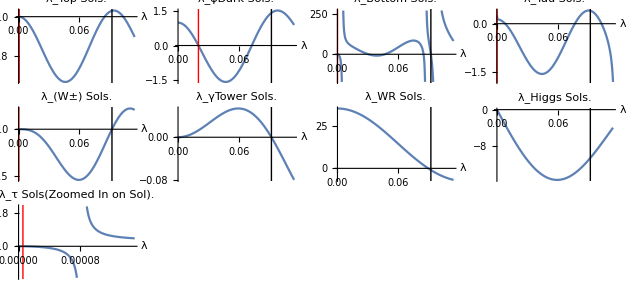

```mathematica
Print["Higgs mass of :           ",Abs[mH]," (GeV)"];
Print["Higgs minimum <θH> is located at :     ",Abs[θHmin]," (rads)"];
Print["---------------------------------------------------------------------------------------------------"]
Print["The 1st KK mode for the top quark: ", toExp["mTop"]];
Print["The 2nd KK mode for the top quark: ", toExp["mTop2"]];
Print["The 1st KK mode for the bottom quark: ", toExp["mBottom"]];
Print["The 1st KK mode for the tau lepton: ", toExp["mTau"]];
Print["The 1st KK mode for the dark fermion multiplet: ", toExp["mPsiDark"]];
Print["The 1st KK mode for the W^(+-) bosons: ", toExp["mWpm"]];
Print["The 1st KK mode for the Z^0 bosons: ", toExp["mZ0"]];
Print["The 2nd KK mode for the Z^0 bosons: ", toExp["mZprime"]];
Print["The 1st KK mode for ν_τ neutrinos: ", toExp["mNeutrino"]];

mKK5Line = InfiniteLine[{mKK5/k,0},{0,1}];
uSolLine = InfiniteLine[{toExp[["mTop"]]/k,0},{0,1}];
psiDarkSolLine =InfiniteLine[{toExp[["mPsiDark"]]/k,0},{0,1}];
bottomQuarkSolLine =InfiniteLine[{toExp[["mBottom"]]/k,0},{0,1}];
tauSolLine=InfiniteLine[{toExp[["mTau"]]/k,0},{0,1}];
wSolLine = InfiniteLine[{toExp[["mWpm"]]/k,0},{0,1}];

HiggsSolTower = Sbasis[λ, z, zLvar] /.replacementRules;
Aνa11SolTower = Cprime[λ, z, zLvar]*Sbasis[λ, z, zLvar] + λ (Sin[θHmin])^2/.replacementRules;


GraphicsGrid[{
{Plot[{uQuarkSol}, {λ, 0, mKK5/k + π/(4zL)} , PlotLegends->"Expressions", Epilog->{{mKK5Line}, {Thick,Red ,uSolLine}}, PlotLabel->"λ_Top Sols.", AxesLabel->Automatic] ,
Plot[{psiDarkQuarkSol}, {λ, 0, mKK5/k + π/(4zL)} , PlotLegends->"Expressions", Epilog->{{mKK5Line}, {Thick,Red ,psiDarkSolLine}}, PlotLabel->"λ_ψDark Sols.", AxesLabel->Automatic],
Plot[{bQuarkSol }, {λ, 0, mKK5/k + π/(4zL)} , PlotLegends->"Expressions" ,Epilog->{{mKK5Line}, {Thick,Red ,bottomQuarkSolLine}}, PlotLabel->"λ_Bottom Sols.",AxesLabel->Automatic], Plot[{ tauLeptonSol}, {λ, 0, mKK5/k + π/(4zL)}  , PlotLegends->"Expressions" ,Epilog->{{mKK5Line}, {Thick,Red ,tauSolLine}}, PlotLabel->"λ_Tau Sols.", AxesLabel->Automatic]},

{Plot[{WbosonSol}, {λ, 0, mKK5/k + π/(4zL)} , PlotLegends->"Expressions", Epilog->{{mKK5Line}, {Thick,Red ,wSolLine}}, PlotLabel->"λ_(W±) Sols.", AxesLabel->Automatic],
Plot[{ γTower}, {λ, 0, mKK5/k + π/(4zL)} , PlotLegends->"Expressions", Epilog->{InfiniteLine[{mKK5/k,0},{0,1}]}, PlotLabel->"λ_γTower Sols.", AxesLabel->Automatic],
Plot[{ WRSol},{λ, 0, mKK5/k + π/(4zL)} , PlotLegends->"Expressions", Epilog->{InfiniteLine[{mKK5/k,0},{0,1}]}, PlotLabel->"λ_WR Sols.", AxesLabel->Automatic],
Plot[{ HiggsSolTower},{λ, 0, mKK5/k + π/(4zL)} , PlotLegends->"Expressions", Epilog->{InfiniteLine[{mKK5/k,0},{0,1}]}, PlotLabel->"λ_Higgs Sols.", AxesLabel->Automatic]},

{
Plot[{tauLeptonSol}, {λ, 0, 0.00015} , PlotLegends->"Expressions", Epilog->{{mKK5Line}, {Thick,Red ,tauSolLine}}, PlotLabel->"λ_τ Sols(Zoomed In on Sol).", AxesLabel->Automatic]
}

}]
```

### Check Higgs, WR and γ solutions as a function of zL

```mathematica
Manipulate[
mKK5 = π k /(zLvar-1);
mKK5Line = InfiniteLine[{mKK5/k,0},{0,1}];
Plot[{ Cbasis[λ, 1, zLvar]},  {λ, 0, mKK5/k + π/(4zL)} , PlotLegends->"Expressions" ,Epilog->{{mKK5Line}}, PlotLabel->"λ_WR Sols.", AxesLabel->Automatic, ImageSize->Small]
Plot[{ Cprime[λ, 1, zLvar]},  {λ, 0, mKK5/k + π/(4zL)} , PlotLegends->"Expressions" ,Epilog->{{mKK5Line}}, PlotLabel->"λ_γ Sols.", AxesLabel->Automatic, ImageSize->Small]
Plot[{Sbasis[λ, 1, zLvar]},  {λ, 0, mKK5/k + π/(4zL)} , PlotLegends->"Expressions" ,Epilog->{{mKK5Line}}, PlotLabel->"λ_Higgs Sols.", AxesLabel->Automatic, ImageSize->Small]
(*Plot[{ Aνa11SolTower},  {λ, 0, mKK5/k + π/(4zL)} , PlotLegends->"Expressions" ,Epilog->{{mKK5Line}}, PlotLabel->"λ_γ Sols.", AxesLabel->Automatic]*)
,{zLvar, 10, 1000}, {k,100000, 300000}
]
```

### Transcendental Equation Manipulation

The transcendental equation is meant to look at C’ basis, and S basis to show that the WR solution (λ cos(λ β) - sin( λ β ) =0 )  is always below the γ solution which is given by π/(zL - 1).

```mathematica
Manipulate[
Plot[{β/x, Tan[x]}, {x, -5 , 5}, Epilog->{{ InfiniteLine[{-π,0},{0,1}]}}]
,{β, -100, 0}
]
```

```mathematica
Manipulate[
mKK5 = π k /(zLvar-1);
mKK5Line = InfiniteLine[{mKK5/k,0},{0,1}];
Plot[{ (2* Cprime[λ, 1, zLvar]*Sbasis[λ, 1, zLvar] + λ (Sin[θHmin])^2), ( Cprime[λ, 1, zLvar]*Sbasis[λ, 1, zLvar] + λ (Sin[θHmin])^2)},  {λ, 0, mKK5/k + π/(4zL)} , PlotLegends->"Expressions" ,Epilog->{{mKK5Line}}, PlotLabel->"λ_(W + -) Sols.", AxesLabel->Automatic, ImageSize->Medium]


(*Plot[{ Aνa11SolTower},  {λ, 0, mKK5/k + π/(4zL)} , PlotLegends->"Expressions" ,Epilog->{{mKK5Line}}, PlotLabel->"λ_γ Sols.", AxesLabel->Automatic]*)
,{zLvar, 10, 1000}, {θHmin, 0.01, π}, {k, 10^5, 2* 10^5}
]
```